```mathematica
mediadir="~/repos/7wonders/media/";
```

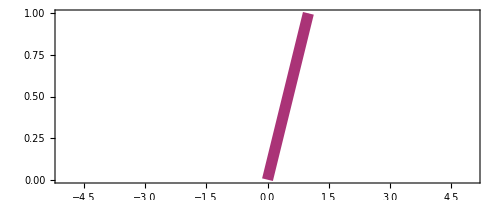

```mathematica
ClearAll[a];tk=0.02;ak=tk*6;
a[x_,y_,dx_,dy_,col_]:={Thickness[tk],Arrowheads[ak],col,Arrow[{{x,y},{x+dx,y+dy}}]};
Graphics[a[0,0,1,1,redpurple],PlotRange->{{-5,5},All},Frame->True]
```

```mathematica
xl=0.4;ay=-0.2;yl=0.0;
tp[i_]=Join[a[#+i,ay+0*Sin[(i+#/2)*2*Pi],xl,yl,purpleblue]]&/@Table[ii,{ii,-12,12,0.5}];
```

```mathematica
he=1.5;
pts=Table[{t/5-0.6,1+0.2*Sin[5*t]},{t,0,2*Pi+Pi/4,Pi/2}];
ClearAll[toplot]
toplot[u_]:={
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{-0,he}}]},

{Thickness[0.01],Arrowheads[0.1],yellow,Arrow[BSplineCurve[pts]]}};


anim=Animate[Graphics[toplot[u],
PlotRange->{{-1,1},{-he,he}},Frame->False],{u,-2,2},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-2},"stop":>{u=2}}]
```

```mathematica
anim=Table[Graphics[toplot[u],PlotRange->{{-1,1},{-he,he}},Frame->False],{u,-2,2,0.1}];
name="pressure";
Export[mediadir<>name<>".mp4",anim,"AnimationDuration"->10];
Export[mediadir<>name<>".webp",anim,"AnimationDuration"->10];
Export[mediadir<>name<>".gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
xl=0.5;ay=-0.3;yl=-0.7;
tp[i_]=Join[a[#+i,ay+0*Sin[(i+#/2)*2*Pi],xl,yl,purpleblue]]&/@Table[ii,{ii,-12,12,0.5}];
```

```mathematica
he=1.5;
pts=Table[{-(t/5-0.6),1+0.2*Sin[5*t]},{t,0,2*Pi+Pi/4,Pi/2}];anim=Animate[Graphics[toplot={
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tp[-u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{-0,he}}]},

{Thickness[0.01],Arrowheads[0.1],yellow,Arrow[BSplineCurve[pts]]}},



PlotRange->{{-1,1},{-he,he}},Frame->False],{u,-2,2},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-2},"stop":>{u=2}}]
```

```mathematica
anim=Table[Graphics[toplot,PlotRange->{{-1,1},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"vectorfluxanim.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"vectorfluxanim.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"vectorfluxanim.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
he=1.5;anim=Animate[Graphics[{Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/vectorfluxanimation.mp4",anim,"AnimationDuration"->10];
Export["media/vectorfluxanimation.webp",anim,"AnimationDuration"->10];
Export["media/vectorfluxanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
xl=0.5;ay=0.5;yl=0;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
he=1;anim=Animate[Graphics[{Text[Style["momentum-flux: pressure",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["momentum-flux: pressure",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/pressureanimation.mp4",anim,"AnimationDuration"->10];
Export["media/pressureanimation.webp",anim,"AnimationDuration"->10];
Export["media/pressureanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
xl=-0.5;ay=0.5;yl=0;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
he=1;anim=Animate[Graphics[{tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["momentum-flux: tension",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/tensionanimation.mp4",anim,"AnimationDuration"->10];
Export["media/tensionanimation.webp",anim,"AnimationDuration"->10];
Export["media/tensionanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
xl=0;ay=0.3;yl=0.5;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,-yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
1;anim=Animate[Graphics[{Text[Style["momentum-flow: shear force",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["momentum-flux: shear force",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/shearforceanimation.mp4",anim,"AnimationDuration"->10];
Export["media/shearforceanimation.webp",anim,"AnimationDuration"->10];
Export["media/shearforceanimation.gif",anim,"AnimationDuration"->10];
```

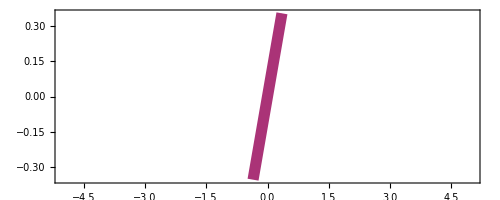

```mathematica
ClearAll[a];tk=0.02;ak=tk*5;
aa[x_,y_,tens_,dir_,col_]:={Thickness[tk],Arrowheads[ak],col,Arrow[{{x-(tens.dir)[[1]]/Norm[dir]/2,y-(tens.dir)[[2]]/Norm[dir]/2},{x+(tens.dir)[[1]]/Norm[dir]/2,y+(tens.dir)[[2]]/Norm[dir]/2}}]};
tens={{1,0},{0,1}}; dir={1,1};
Graphics[aa[0,0,tens,dir,redpurple],PlotRange->{{-5,5},All},Frame->True]
```

```mathematica
xl=-0.2;ay=0.3;yl=0.7;
le=1.5;
shi=1;amp=0;he=2;
tens=0.3*{{3,-2},{-2,-1}};
dir1=((#/Norm[#])&@{1,0});
dir2=((#/Norm[#])&@{0,1});
Clear[tpp];
tpp[u_,dir_]:=Join[aa[
(#+u)*dir[[1]]
+(shi+amp*Sin[(#+u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[1]],
(#+u)*dir[[2]]
+(shi+amp*Sin[(#+u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[2]],
tens,dir,purpleblue],
aa[
(#-u)*dir[[1]]
-(shi+amp*Sin[(#-u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[1]],
(#-u)*dir[[2]]
-(shi+amp*Sin[(#-u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[2]],
tens,-dir,redpurple]]&/@Table[ii,{ii,-12,12,0.5}];
ani[dir_]:=Animate[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->True],{u,-2,2},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-2},"stop":>{u=2}}];
```

```mathematica
{ani[dir1],ani[dir2]}
```

{,}

```mathematica
dir=dir1;anim=Table[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"skewflux1.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"skewflux1.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"skewflux1.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
dir=dir2;anim=Table[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"skewflux2.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"skewflux2.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"skewflux2.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
xl=-0.2;ay=0.3;yl=0.7;
le=1.5;
shi=-1;amp=0.05;he=2;
tens=0.75*{{0,1},{1,0}};
dir1=((#/Norm[#])&@{1,0});
dir2=((#/Norm[#])&@{0,1});
Clear[tpp];
tpp[u_,dir_]:=Join[aa[
(#+u)*dir[[1]]
+(shi+amp*Sin[(#+u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[1]],
(#+u)*dir[[2]]
+(shi+amp*Sin[(#+u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[2]],
tens,dir,redpurple],
aa[
(#-u)*dir[[1]]
-(shi+amp*Sin[(#-u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[1]],
(#-u)*dir[[2]]
-(shi+amp*Sin[(#-u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[2]],
tens,-dir,redpurple]]&/@Table[ii,{ii,-12,12,1}];
ani[dir_]:=Animate[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[-u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->True],{u,-2,2},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-2},"stop":>{u=2}}];
```

```mathematica
{ani[dir1],ani[dir2]}
```

{,}

```mathematica
dir=dir2;anim=Table[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[-u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"shearforceH.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"shearforceH.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"shearforceH.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
dir=dir2;anim=Table[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[-u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"test.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"test.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"test.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
tens.dir1//MF
```

(0.9
-0.6)

```mathematica
tens.dir2//MF
```

(-0.6
-0.3)

```mathematica
Norm[tens.dir1*10]
```

10.8167

```mathematica
Norm[tens.dir2*10]
```

6.7082

```mathematica
(* With oscillations *)
```

```mathematica
mediadir="~/repositories/7wonders/media/";
```

```mathematica
ClearAll[a];tk=0.02;ak=tk*6;
a[x_,y_,dx_,dy_,col_]:={Thickness[tk],Arrowheads[ak],col,Arrow[{{x,y},{x+dx,y+dy}}]};
Graphics[a[0,0,1,1,redpurple],PlotRange->{{-5,5},All},Frame->True]
```

-Graphics-

```mathematica
xl=-0.2;ay=0.3;yl=0.7;
tp[i_]=Join[a[#+i,ay+0.1*Sin[(i+#/2)*2*Pi],xl,yl,purpleblue],a[#-i,-ay+0.1*Sin[(i+#/2)*2*Pi],-xl,-yl,redpurple]]&/@Table[ii,{ii,-12,12,0.5}];
```

```mathematica
he=1.5;anim=Animate[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0.2,-he},{-0.2,he}}]}},PlotRange->{{-1,1},{-he,he}},Frame->False],{u,-2,2},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-2},"stop":>{u=2}}]
```

```mathematica
anim=Table[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0.2,-he},{-0.2,he}}]}},PlotRange->{{-1,1},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"vectorfluxanimsin.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"vectorfluxanimsin.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"vectorfluxanimsin.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
he=1.5;anim=Animate[Graphics[{Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/vectorfluxanimation.mp4",anim,"AnimationDuration"->10];
Export["media/vectorfluxanimation.webp",anim,"AnimationDuration"->10];
Export["media/vectorfluxanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
xl=0.5;ay=0.5;yl=0;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
he=1;anim=Animate[Graphics[{Text[Style["momentum-flux: pressure",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["momentum-flux: pressure",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/pressureanimation.mp4",anim,"AnimationDuration"->10];
Export["media/pressureanimation.webp",anim,"AnimationDuration"->10];
Export["media/pressureanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
xl=-0.5;ay=0.5;yl=0;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
he=1;anim=Animate[Graphics[{tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["momentum-flux: tension",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/tensionanimation.mp4",anim,"AnimationDuration"->10];
Export["media/tensionanimation.webp",anim,"AnimationDuration"->10];
Export["media/tensionanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
xl=0;ay=0.3;yl=0.5;
tp[i_]=Join[a[#+i,ay,xl,yl,purpleblue],a[#-i,-ay,-xl,-yl,redpurple]]&/@Table[i,{i,-12,12,0.75}];
```

```mathematica
1;anim=Animate[Graphics[{Text[Style["momentum-flow: shear force",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-5},"stop":>{u=5}}]
```

```mathematica
anim=Table[Graphics[{Text[Style["momentum-flux: shear force",20,FontFamily->"Palatino LT Std"]],tp[u],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{{0,-he},{0,he}}]}},PlotRange->{{-2,2},{-he,he}},Frame->False],{u,-5,5,0.1}];
Export["media/shearforceanimation.mp4",anim,"AnimationDuration"->10];
Export["media/shearforceanimation.webp",anim,"AnimationDuration"->10];
Export["media/shearforceanimation.gif",anim,"AnimationDuration"->10];
```

```mathematica
ClearAll[a];tk=0.02;ak=tk*5;
aa[x_,y_,tens_,dir_,col_]:={Thickness[tk],Arrowheads[ak],col,Arrow[{{x-(tens.dir)[[1]]/Norm[dir]/2,y-(tens.dir)[[2]]/Norm[dir]/2},{x+(tens.dir)[[1]]/Norm[dir]/2,y+(tens.dir)[[2]]/Norm[dir]/2}}]};
tens={{1,0},{0,1}}; dir={1,1};
Graphics[aa[0,0,tens,dir,redpurple],PlotRange->{{-5,5},All},Frame->True]
```

-Graphics-

```mathematica
xl=-0.2;ay=0.3;yl=0.7;
le=1.5;
shi=1;amp=0.05;he=2;
tens=0.3*{{3,-2},{-2,-1}};
dir1=((#/Norm[#])&@{1,0});
dir2=((#/Norm[#])&@{0,1});
Clear[tpp];
tpp[u_,dir_]:=Join[aa[
(#+u)*dir[[1]]
+(shi+amp*Sin[(#+u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[1]],
(#+u)*dir[[2]]
+(shi+amp*Sin[(#+u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[2]],
tens,dir,purpleblue],
aa[
(#-u)*dir[[1]]
-(shi+amp*Sin[(#-u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[1]],
(#-u)*dir[[2]]
-(shi+amp*Sin[(#-u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[2]],
tens,-dir,redpurple]]&/@Table[ii,{ii,-12,12,0.5}];
ani[dir_]:=Animate[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->True],{u,-2,2},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-2},"stop":>{u=2}}];
```

```mathematica
{ani[dir1],ani[dir2]}
```

{,}

```mathematica
dir=dir1;anim=Table[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"skewflux1.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"skewflux1.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"skewflux1.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
dir=dir2;anim=Table[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"skewflux2.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"skewflux2.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"skewflux2.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
xl=-0.2;ay=0.3;yl=0.7;
le=1.5;
shi=-1;amp=0.05;he=2;
tens=0.75*{{0,1},{1,0}};
dir1=((#/Norm[#])&@{1,0});
dir2=((#/Norm[#])&@{0,1});
Clear[tpp];
tpp[u_,dir_]:=Join[aa[
(#+u)*dir[[1]]
+(shi+amp*Sin[(#+u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[1]],
(#+u)*dir[[2]]
+(shi+amp*Sin[(#+u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[2]],
tens,dir,redpurple],
aa[
(#-u)*dir[[1]]
-(shi+amp*Sin[(#-u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[1]],
(#-u)*dir[[2]]
-(shi+amp*Sin[(#-u)*2*Pi])*(RotationMatrix[Pi/2].dir)[[2]],
tens,-dir,redpurple]]&/@Table[ii,{ii,-12,12,1}];
ani[dir_]:=Animate[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[-u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->True],{u,-2,2},AnimationRate->1,AppearanceElements->None,Bookmarks->{"start":>{u=-2},"stop":>{u=2}}];
```

```mathematica
{ani[dir1],ani[dir2]}
```

{,}

```mathematica
dir=dir2;anim=Table[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[-u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"shearforceH.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"shearforceH.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"shearforceH.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
dir=dir2;anim=Table[Graphics[{
(*Text[Style["flux of a vector quantity",20,FontFamily->"Palatino LT Std"]],*)tpp[-u,dir],{Thickness[0.04],Opacity[0.5],GrayLevel[0.1],Line[{2*RotationMatrix[Pi/2].dir,-2*RotationMatrix[Pi/2].dir}]}},PlotRange->{{-he,he},{-he,he}},Frame->False],{u,-2,2,0.1}];
Export[mediadir<>"test.mp4",anim,"AnimationDuration"->10];
Export[mediadir<>"test.webp",anim,"AnimationDuration"->10];
Export[mediadir<>"test.gif",anim,"AnimationDuration"->10,RasterSize->Medium];
```

```mathematica
tens.dir1//MF
```

(0.9
-0.6)

```mathematica
tens.dir2//MF
```

(-0.6
-0.3)

```mathematica
Norm[tens.dir1*10]
```

10.8167

```mathematica
Norm[tens.dir2*10]
```

6.7082